# FernandoDuarte/LongRunRisk

Tools to solve and analyze long-run risk models

## Paclet Manifest

"Documentation"

"English"

"Guides"

"MainGuide.nb"DocumentationEnglishGuidesMainGuide.nb

"ReferencePages"

"Tutorials"

"TimeAggregation.nb"DocumentationEnglishTutorialsTimeAggregation.nb

"Kernel"

"ComputationalEngine.wl"KernelComputationalEngine.wl

"LongRunRisk.wl"KernelLongRunRisk.wl

"Model"

"Catalog.wl"KernelModelCatalog.wl

"EndogenousEq.wl"KernelModelEndogenousEq.wl

"ExogenousEq.wl"KernelModelExogenousEq.wl

"NiceOutput.wl"KernelModelNiceOutput.wl

"Parameters.wl"KernelModelParameters.wl

"Shocks.wl"KernelModelShocks.wl

"PacletizeResources.wl"KernelPacletizeResources.wl

"TimeAggregation.wl"KernelTimeAggregation.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

"Resources"

"BibTeX"

"references.bib"ResourcesBibTeXreferences.bib

"Paclets"

"Tests"

"Catalog.nb"TestsCatalog.nb

"Catalog.wlt"TestsCatalog.wlt

"ComputationalEngine.nb"TestsComputationalEngine.nb

"EndogenousEq.nb"TestsEndogenousEq.nb

"ExogenousEq.nb"TestsExogenousEq.nb

"ModelEngine.nb"TestsModelEngine.nb

"NiceOutput.nb"TestsNiceOutput.nb

"PacletizeResources.nb"TestsPacletizeResources.nb

"RunAllTests.nb"TestsRunAllTests.nb

"Shocks.nb"TestsShocks.nb

"Shocks.wlt"TestsShocks.wlt

"TimeAggregation.nb"TestsTimeAggregation.nb

"TimeAggregationToAdapt.nb"TestsTimeAggregationToAdapt.nb

"TimeAggregation.wlt"TestsTimeAggregation.wlt

## Web Content

### Headline Image

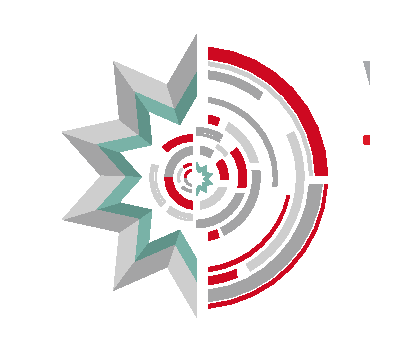

```mathematica
url="https://www.wolfram.com/events/technology-conference/2022/img/WTC-2022-date.svg";
svg=ResourceFunction["SVGImport"][url];
Show[svg,PlotRange->{{-25,385},{0,360}},ImageSize->Automatic]
```

### Basic Description

Tools to solve and analyze long-run risk models.

### Details

Solves long-run risk type models

Performs approximate time-aggregation

Computes moments

### Main Guide Page

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["FernandoDuarte`LongRunRisk`"];
```

## Examples

### Basic Examples

Show a table with information of the available models (takes a bit of time to load the first time):

```mathematica
Models
```

Models are defined by their parameters and state variables in an Association. We can also specify name, description, etc. Here is the Association that defines one of the models:

```mathematica
m=Models["BY"]
```

<|name→Original long-run risk model,shortname→BY,bibRef→BY2004,desc→Long-run risk model with stochastic				
			volatility in the original 2004 paper by
							Bansal and Yaron,stateVars→{x[t],sx[t]},parameters→{delta→0.998,psi→1.5,gamma→10,theta→(1-gamma)/(1-1/psi),rhox→0.979,rhoxpbar→0,phix→0.044,phixc→0,mup→0,rhoppbar→0,rhop→0,phip→0,xip→0,phipc→0,phipx→0,phipcx→0,phipp→0,phipxp→0,mupbar→0,rhopbar→0,rhopbarx→0,phipbarp→0,phipbarc→0,phipbarx→0,phipbarcx→0,phipbarpb→0,phipbarxb→0,phipbarxp→0,muc→0.0015,rhocx→1,rhocp→0,phic→0,phicp→0,phicsp→0,xic→0,phics→0,phicx→1,phicc→0,phicpc→0,phicpp→0,Esg→0,rhog→0,phig→0,Esx→0.0078,vx→0.987,phisxs→2.3×10^-6,Esc→0,vc→0,phiscv→0,Esp→0,vp→0,vpp→0,vppbar→0,phispw→0,mud[1]→0.0015,rhodx[1]→3,rhodp[1]→0,phidc[1]→0,phidp[1]→0,phidsp[1]→0,xid[1]→0,phids[1]→0,phidxc[1]→0,phidcc[1]→0,phidpc[1]→0,phidpp[1]→0,phidxd[1]→4.5,phidcd[1]→0,phidpd[1]→0,taugd[1]→0}|>

Extract properties and use them:

```mathematica
param=m["parameters"]
```

{delta→0.998,psi→1.5,gamma→10,theta→(1-gamma)/(1-1/psi),rhox→0.979,rhoxpbar→0,phix→0.044,phixc→0,mup→0,rhoppbar→0,rhop→0,phip→0,xip→0,phipc→0,phipx→0,phipcx→0,phipp→0,phipxp→0,mupbar→0,rhopbar→0,rhopbarx→0,phipbarp→0,phipbarc→0,phipbarx→0,phipbarcx→0,phipbarpb→0,phipbarxb→0,phipbarxp→0,muc→0.0015,rhocx→1,rhocp→0,phic→0,phicp→0,phicsp→0,xic→0,phics→0,phicx→1,phicc→0,phicpc→0,phicpp→0,Esg→0,rhog→0,phig→0,Esx→0.0078,vx→0.987,phisxs→2.3×10^-6,Esc→0,vc→0,phiscv→0,Esp→0,vp→0,vpp→0,vppbar→0,phispw→0,mud[1]→0.0015,rhodx[1]→3,rhodp[1]→0,phidc[1]→0,phidp[1]→0,phidsp[1]→0,xid[1]→0,phids[1]→0,phidxc[1]→0,phidcc[1]→0,phidpc[1]→0,phidpp[1]→0,phidxd[1]→4.5,phidcd[1]→0,phidpd[1]→0,taugd[1]→0}

```mathematica
delta/.param
```

0.998

Get more information about a model:

```mathematica
fillm=fillModels[models];
fillm["BY"]
```

fillModels[models][BY]

Create a very interesting Plot:

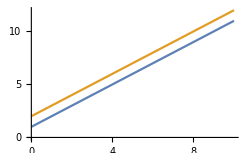

```mathematica
Plot[{AddOne[x],AddTwo[x]},{x,0,10}]
```

### Scope

Add to symbols:

```mathematica
AddOne[x]
```

1+x

```mathematica
AddTwo[x]
```

2+x

Create new functions that no one has ever thought of before:

```mathematica
addThree=AddOne@*AddTwo
```

AddOne@*AddTwo

```mathematica
addThree[1]
```

4

```mathematica
naturalNumber[n_]:=Nest[AddOne,0,n];
```

Simply incredible:

```mathematica
naturalNumber[5]
```

5

### Applications

Reinvent arithmetic:

```mathematica
plus[x_,y_]:=Nest[AddOne,x,y];
```

```mathematica
plus[3,4]
```

7

```mathematica
times[x_,y_]:=Nest[OperatorApplied[plus][x],0,y];
```

```mathematica
times[3,4]
```

12

Weird numbers like negative integers and reals are too hard and can therefore be assumed to not exist.

### Properties and Relations

AddTwo can be implemented using only AddOne:

```mathematica
AddTwo[x]
```

2+x

```mathematica
addTwo=AddOne@*AddOne;
```

```mathematica
addTwo[x]
```

2+x

AddOne is the best function:

```mathematica
[Row[{AddOne," is simply the best"}]]
```

-Graphics-

## Source & Additional Information

### Creator

Fernando Duarte

### Source Control Repository

https://github.com/GitHub-at-Brown/LongRunRisk

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Economics

Finance

Asset Pricing

CI/CD

GitHub

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

### Original Source References and Attributions

Source, reference or citation

### Links

GitHub

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.